```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/mcmcclur/GitHubDocuments/MarksMath/writ/MapProjection/newerFigures

```mathematica
landData = Import["ne_110m_land-geo.json"];
parallels=Line[Table[Table[{lng,lat},{lng,-180,180,5}],{lat,-85,85,10}]];
meridians=Line[Table[Table[{lng,lat},{lat,-85,85,5}],{lng,-180,180,10}]];
land = Map[Polygon["coordinates" /. #]&, "geometry" /. ("features" /. landData)];
```

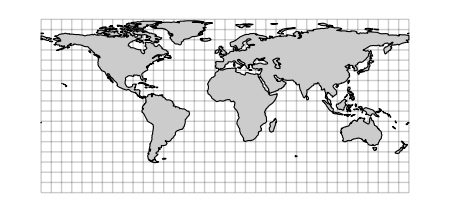

```mathematica
im = Graphics[{{Opacity[0.2],parallels, meridians}, {GrayLevel[0.8],EdgeForm[Black],land}}, ImageSize -> 450]
```

```mathematica
globe = ParametricPlot3D[{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]} ,
{u,0,2Pi},{v, 0,Pi}, Mesh->None,PlotPoints->100,
TextureCoordinateFunction->({#4,1-#5}&), Boxed->False,
PlotStyle->Texture[Show[im,ImageSize->1000]],
Axes->False,RotationAction->"Clip",
ViewPoint -> {-2.026774,2.07922,1.73753418},
ImageSize->500]
```

-Graphics3D-

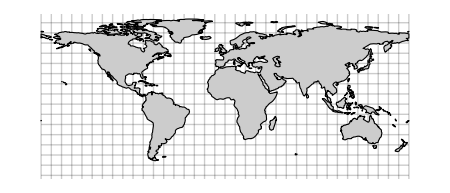
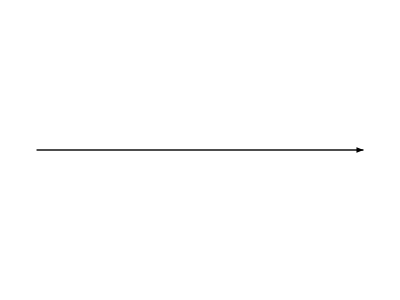
-Graphics3D- | -Graphics--Graphics-

```mathematica
Overlay[{
Grid[{{globe,Show[im, PlotRange -> {{-180,180},{-70,85}}]}},Spacings->4],
Graphics[{Arrow[{{-3,0},{0.5,0}}]}, PlotRange -> 10]},
Alignment->Center]
```

```mathematica
im /. {
Polygon[pts_] :> Polygon[Map[{#[[1]], Log[Abs[Sec[#[[2]]*Degree]+Tan[#[[2]]*Degree]]]/Degree}&, pts,{2}]],
Line[pts_] :> Line[Map[{#[[1]], Log[Abs[Sec[#[[2]]*Degree]+Tan[#[[2]]*Degree]]]/Degree}&, pts, {1}]]
}
```

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

-Graphics-

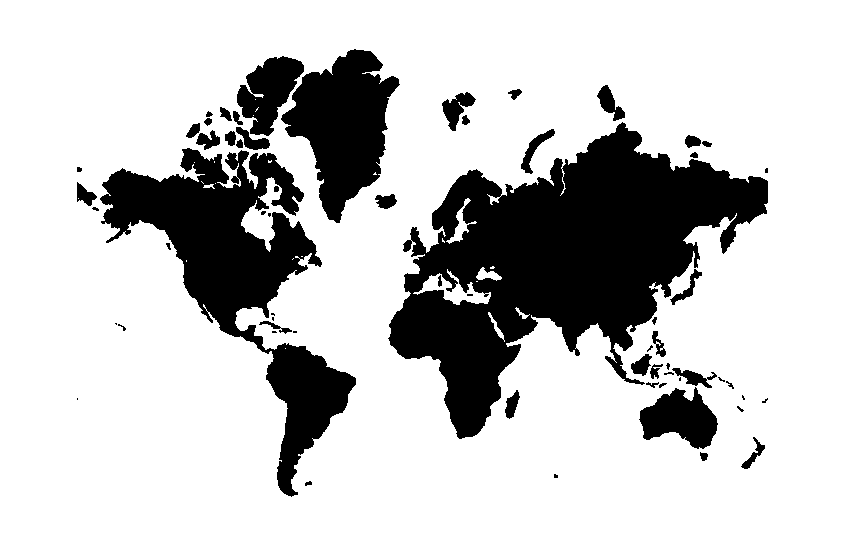

```mathematica
Graphics[Cases[im, 
Polygon[pts_] :> Polygon[Map[{#[[1]], Log[Abs[Sec[#[[2]]*Degree]+Tan[#[[2]]*Degree]]]/Degree}&, pts,{2}]]
, Infinity]]
```

```mathematica
Degree//N
```

0.0174533